```mathematica
Subscript[ϕ, n_][x_] = 1/π^(1/4)/Sqrt[2^n*Factorial[n]] * HermiteH[n,x]*E^(-x^2/2);
b[t_]=Sqrt[1+t^2];
τ[t_]=ArcTan[t];
Subscript[Φ, n_][x_,t_]=b[t]^(-1/2)Subscript[ϕ, n][x/b[t]]*E^(I*(x^2*b'[t]/(2*b[t])-(n+1/2)τ[t]));
t ≥0;
Subscript[ψ, F][x_,y_,t_] = 1/Sqrt[2] * (Subscript[Φ, 0][x,t]Subscript[Φ, 1][y,t] - Subscript[Φ, 0][y,t]Subscript[Φ, 1][x,t] );
Subscript[ρ, F][x_,y_]=Integrate[Subscript[ψ, F][x,Subscript[x, 2],0]*Subscript[ψ, F][y,Subscript[x, 2],0],{Subscript[x, 2],-Infinity,Infinity}];
Subscript[ψ, A][x_,y_,t_,κ_]=E^(I*π*(1-κ)HeavisideTheta[y-x])Subscript[ψ, F][x,y,t];
Subscript[ρ, α][x_,y_,κ_]=Subscript[ρ, F][x,y]-Sign[y-x]*(E^(-Sign[y-x]*I*π*κ)+1)*Integrate[Subscript[ψ, F][x,Subscript[x, 2],0]*Subscript[ψ, F][y,Subscript[x, 2],0], {Subscript[x, 2],x, y}];
Subscript[ρ, A][x_,y_,t_,κ_]=1/b[t]*Subscript[ρ, α][x/b[t],y/b[t],κ]*E^((I*b'[t])/(2b[t])(y^2-x^2));
Subscript[n, A][p_,t_,κ_]:=2/(2π)NIntegrate[E^(I*p*(x-y))Subscript[ρ, A][x,y,t,κ],{x,-∞, ∞},{y,-∞, ∞},Method->{"LocalAdaptive", Method->"CartesianRule"}, AccuracyGoal->5,PrecisionGoal->5];
```

```mathematica
Subscript[n, F][p_] = 2/(2*π)*Integrate[E^(-I*p*(y-x))*Subscript[ρ, F][x,y],{x,-∞, ∞},{y,-∞, ∞}];
```

```mathematica
Pdomain=Union[Range[-4,-2,1/2],Range[-2,2,1/3],Range[2,4,1/2]];
(*Tdomain = {0,0.25,.5,0.75,1,1.5,2,2.5,3,3.5,4,5,6,7,8,9,10,12};*)
Tdomain={0,.5,1,2,4,8,12};
(* Set interopolation functions for various points in time *)
Subscript[dataSet, m_]:=Re[Subscript[n, A][Pdomain,Tdomain[[m]] ,1/2]];
(*Do[Subscript[dataSet, i]=Subscript[dataSet, i],{i,1,Length[Tdomain]}]*)
(* Prepare domains and ranges for plotting*)
FullD=Pdomain;
Do[Subscript[FullR, i]=Subscript[dataSet, i],{i,1,Length[Tdomain]}];
(* create list of interpolated functions for plotting purposes *)
Do[Subscript[f, i]=Interpolation[Thread[{FullD,Subscript[FullR, i]}] ],{i,1,Length[Tdomain]}]
```

```mathematica
frame[i_]:=Show[Plot[{Subscript[f, i][x],Subscript[n, F][x]},{x,-4,4},PlotStyle -> {{Default, Thickness[0.005]}, {Dashed, Red, Thickness[.003]}},PlotRange->{0,1.2},PlotStyle -> {Default,Dashed},PlotLabel->"Momentum Distribution: Expanding Gas of HC Anyons κ=1/2",AxesLabel->{"p","n_A(p,t)"},ImageSize->Scaled[1], AxesStyle->Thickness[.0015]],Graphics[Text[StringForm["t = ``",Tdomain[[i]]],{1.5,1},{0,0}]]];
frames=Table[frame[i],{i,1,Length[Tdomain]}];
Export["C:/Users/Tim/Documents/PhysicsResearch/UltraColdAtoms/Plots/ExpandingAnyonGasPoster.gif",frames,AnimationRepetitions->Infinity,"DisplayDurations"-> .25];
```

```mathematica
Subscript[dataSet, 1]={0.0015587243725541152,0.0031314770872042257,0.006484316163300792,0.012491250377929822,0.03658947770049151,0.10712044954682069,0.28494425474201135,0.5840991497479183,0.8894848918117619,1.0026241268250347,0.8510742947132526,0.591342009842938,0.42047810663238927,0.3630647081395117,0.32053176587532206,0.2380221749859197,0.14144103377043676,0.045425025552733485,0.011918055200025056,0.0036791075276141737,0.0015956915885461654};
Subscript[dataSet, 2]={0.0010419611007169442,0.0022060555122537097,0.005898136356215865,0.017209010694640037,0.055287267066483944,0.13299405497732014,0.3036473565979649,0.5752245803175692,0.8441923043646468,0.9384163568149078,0.804021187680067,0.5879851400575471,0.45669355492839603,0.41106189844659513,0.35398322874280475,0.24889894980586133,0.13716237197420403,0.0370993067474083,0.007753359317195976,0.0022064098640353336,0.001031086377301028};
Subscript[dataSet, 3]={0.0004669536687268113,0.0009637543309628389,0.003633975779641247,0.01942730753120385,0.08103534792722897,0.17745233044838182,0.3435754946686342,0.5702611884443192,0.7727745595433797,0.8298466071627438,0.7245342920898536,0.5863461771192391,0.5234450666904998,0.49269697756328157,0.4031129204785562,0.2565591545789586,0.12285931682229816,0.02415908624862707,0.003395698339130148,0.0009223272378941117,0.0004672558642916666};
Subscript[dataSet, 4]={0.00011194226987739087,0.0002699107374170203,0.0017532391060956466,0.016082500397470438,0.09406417655220185,0.22005699491618877,0.40242928350822776,0.5894991936637938,0.7040160531154521,0.7008200403563115,0.6293938646878317,0.595533513302804,0.6151236033639469,0.5834858964956596,0.4370453500633876,0.24404340359699234,0.10079226181029091,0.01601369111640878,0.0017286596695171032,0.0002707348909929579,0.00011186975772502907};
Subscript[dataSet, 5]={-0.000011027336035439945,0.00010067843988387054,0.0013794266890633457,0.014873965412999464,0.09342489066682491,0.22931917454680345,0.4293897595570698,0.6140738001969062,0.6843717049534996,0.6355228241273244,0.5792287816333326,0.6098229290337011,0.6678177867551799,0.6173093687515465,0.436797752614078,0.23244607271902798,0.09396166877845438,0.014835157239573224,0.0013861798911582314,0.00011428028351869157,0.000016197204130912322};
Subscript[dataSet, 6]={-0.00017151397463208682,0.00003542375233324256,0.0011231053569276247,0.01470812514756747,0.09299558699189281,0.2300593393691931,0.4339641265211741,0.621212950706647,0.6833873531882272,0.6203231880472996,0.5663875939930015,0.6156037071690728,0.6808640719754087,0.6219463178801399,0.4347741989193073,0.23016358777943474,0.09315643123487226,0.014708679211544602,0.0012958391356311415,-0.00012777585732830034,-0.000041827955617554764};
Subscript[dataSet, 7]={-0.001170297267563438,0.00009327101309821782,0.0018820254022554037,0.014432790733645146,0.09101625859430801,0.23028129826328034,0.43531901153006813,0.6218473434206852,0.6834242281855523,0.6193634517954274,0.5632680140576114,0.6177065372812314,0.6828791247078924,0.6222381535848134,0.4365760404818701,0.22796456854885094,0.09299667968295515,0.014513022467992161,0.0020408832534681153,0.0004345950647007613,0.0001949459235771911};
```

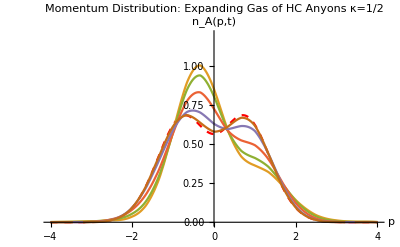

```mathematica
FuncList=Take[Join[{Subscript[n, F][x]},Array[Subscript[f, #][x]&,Length[Tdomain],1]],6];
p2=Plot[FuncList,{x,-4,4},PlotRange->{0,1.2},PlotStyle -> {{Dashed,Red},Default,Default,Default,Default,Default},PlotLabel->"Momentum Distribution: Expanding Gas of HC Anyons κ=1/2",AxesLabel->{"p","n_A(p,t)"},ImageSize->Scaled[1.]]
(*Export["C:/Users/Tim/Documents/PhysicsResearch/UltraColdAtoms/Plots/MomDistExpandingAG.png",p2]*)
```

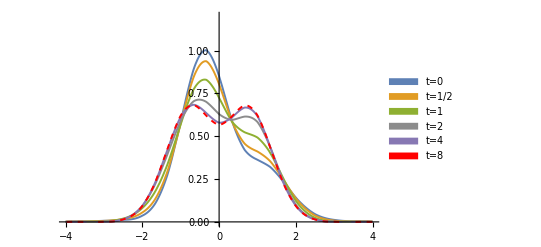

C:/Users/Tim/Documents/PhysicsResearch/UltraColdAtoms/Poster/MomDistExpandingAG.png

```mathematica
FuncList=Take[Join[Array[Subscript[f, #][x]&,Length[Tdomain],1],{Subscript[n, F][x]}],6];
p2=Plot[FuncList,{x,-4,4},PlotRange->{0,1.2},PlotStyle -> {Thickness[.0035],Thickness[.0035],Thickness[.0035],{Thickness[.0035],GrayLevel[0.55]},Thickness[.0035],{Dashing[.01],Red, Thickness[.0035]}},ImageSize->Scaled[1.5],BaseStyle->{FontWeight->Bold,FontFamily-> "Helvetica",FontSize-> 40},AxesStyle->Thick,
PlotLegends->SwatchLegend[{"t=0", "t=1/2","t=1","t=2","t=4","t=8", "t -> infty(Fermions)"},LabelStyle->{FontWeight->Bold,FontFamily-> "Helvetica",FontSize-> 24}]]
Export["C:/Users/Tim/Documents/PhysicsResearch/UltraColdAtoms/Plots/MomDistExpandingAG.png",p2]
```

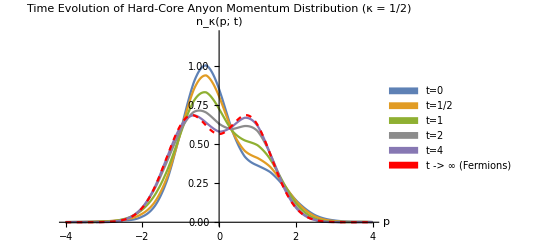

C:/Users/tskar/Documents/PhysicsResearch/UltraColdAtoms/Plots/MomDistExpandingAG-Proposal.png

```mathematica
FuncList=Join[Take[Array[Subscript[f, #][x]&,Length[Tdomain],1],5],{Subscript[n, F][x]}];
p2=Plot[FuncList,{x,-4,4},PlotRange->{0,1.2},PlotStyle -> {Default,Default,Default,GrayLevel[0.55],Default,{Dashing[.01],Red}},ImageSize->Scaled[0.5],BaseStyle->{FontWeight->Bold,FontFamily-> "Helvetica",FontSize-> 12},AxesStyle->Thick,
AxesLabel->{"p", "n_κ(p; t)"},
PlotLabel->"Time Evolution of Hard-Core Anyon Momentum Distribution (κ = 1/2)",
PlotLegends->SwatchLegend[{"t=0", "t=1/2","t=1","t=2","t=4", "t -> ∞ (Fermions)"},LabelStyle->{FontWeight->Bold,FontFamily-> "Helvetica",FontSize-> 12}]]
Export["C:/Users/tskar/Documents/PhysicsResearch/UltraColdAtoms/Plots/MomDistExpandingAG-Proposal.png",p2]
```